# Forecasting risk under temporal autocorrelation

Code for forecasting long-term extinction risk under different levels of temporal autocorrelation given an organism’s thermal performance curve (TPC), compared to weak and strong persistence boundaries calculated as in Vasseur et al. (2025). This notebook contains all the code used to generate the simulations and create Fig. 1 in Robey et al. 2025; for easy replication of that figure, download the required MX files from the repository beforehand (SDE10000_gamma0, 1, and 2.m; windowing_r100_l10000_white, pink, and brown.m). Subfigures from this notebook were combined into one figure using Adobe Acrobat 2024.

## Background Functions

Initialize functions for spectral synthesis, which generates a series with a specified level of autocorrelation ‘γ’, length ‘Nobs’, mean ‘μ’, and standard deviation ‘σ’ using an inverse Fourier transformation.

```mathematica
cmplx[mod_,arg_]:=ExpToTrig[mod Exp[I arg]];

SpecSynFourier[γ_,Nobs_,μ_:0,σ_:1,seed_:0]:=Module[{
phase,f,vec},
If[seed==0,SeedRandom[],SeedRandom[seed]];
phase=RandomReal[{0,2Pi},Nobs];
f=Range[1/Nobs,1,1/Nobs];
vec=InverseFourier[Join[{0+0I},Table[cmplx[1/(f[[i]]^(γ/2)),phase[[i]]],{i,1,(Nobs-1)}]],FourierParameters->{-1,1}];
Standardize[Re[vec]]*σ+μ];
```

Initialize the ‘Lactin2’ TPC (parameterized for P. caudatum; Lactin et al, 1995) and calculate the statistical moments, which are used to generate the persistence boundaries (Vasseur et al. 2025). Edit the ‘directory’ line before any of the rest of the code to specify the location simulations should be exported to and/or imported from.

```mathematica
directory="/home/ajr222/outputs/";

lactin2[T_,{a_,b_,tmax_,δT_}]:=Exp[a T]-Exp[a tmax-((tmax-T)/δT)]+b;
paramsfit={0.044,-1.774,35.254,5.435};

w[T_]:=lactin2[T,paramsfit];

divisions=40;
σTrange=Range[0.01,8.01,8/divisions];
μTrange=Range[10,35,25/divisions];
Clear[T];
moments=Flatten[ParallelTable[Module[{mean,var,skew,kurt},
mean=NExpectation[w[T],T\[Distributed]NormalDistribution[μT,σT]];var=NExpectation[(w[T]-mean)^2,T\[Distributed]NormalDistribution[μT,σT]];
skew=NExpectation[((w[T]-mean))^3,T\[Distributed]NormalDistribution[μT,σT]]/var^(3/2);
kurt=NExpectation[(w[T]-mean)^4,T\[Distributed]NormalDistribution[μT,σT]]/(var^2)-3;
{μT,σT,mean,var,skew,kurt,If[mean>0,Log10[var/mean],10]}],{σT,σTrange},{μT,μTrange}],1];
```

## SDE Model

Runs simulations and stores extinction outcomes. ‘EMproc2’ is Equ. 2 and ‘SpecSynFourier’ generates a temperature time series with the specified parameters. To run simulations shown in paper, use parameters in parentheses after setting γ to the desired spectral exponent (best done on a computing cluster, these take a long time!); if you have already downloaded the MX files, skip to the next block of code.

```mathematica
EMproc2[n_,T_]:=n+(w[T] n-α n^2) δt;
tmax=10000; (*10000*)
δt=0.01; (*.01*)
α=0.0001;(*0.0001*)
reps=100; (*100*)
γ=2; (*set autocorrelation level here*)

output=Flatten[
ParallelTable[
Module[{
extinct=0},
Do[
p=NExpectation[w[x],x\[Distributed] NormalDistribution[μT,σT]]/α;
T=SpecSynFourier[γ,(tmax/δt),μT,σT];
Do[p=EMproc2[p,T[[i]]];
If[p<1,extinct++;Break[]],{i,1,tmax/δt}];,{reps}];

{μT,σT,1-extinct/reps}]
,{σT,σTrange},{μT,μTrange}],1];

Export[directory<>"SDE"<>ToString[tmax]<>"_gamma"<>ToString[γ]<>".m",output,"MX"]
```

Download the needed MX files and generate plots shown in Fig. 1a-c.

```mathematica
SDEwhite=Import[directory<>"SDE10000_gamma0.m","MX"];
SDEpink=Import[directory<>"SDE10000_gamma1.m","MX"];
SDEbrown=Import[directory<>"SDE10000_gamma2.m","MX"];

newmap[x_]:=Blend[{RGBColor["#ffffd9"],RGBColor["#edf8b1"],RGBColor["#c7e9b4"],RGBColor["#7fcdbb"],RGBColor["#41b6c4"],RGBColor["#4eb3d3"],RGBColor["#2b8cbe"],RGBColor["#0868ac"],RGBColor["#084081"]},1-x];

SDEwhiteplot=Show[ListContourPlot[SDEwhite,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Proportion\n Persisting",LabelStyle->{Darker[Gray],13}],Left],PlotLabel->Style["White Noise (γ = 0)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->{{Text[Style["a)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];
SDEpinkplot=Show[ListContourPlot[SDEpink,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLabel->Style["Pink Noise (γ = 1)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],Epilog->{{Text[Style["b)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];
SDEbrownplot=Show[ListContourPlot[SDEbrown,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLabel->Style["Brown Noise (γ = 2)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],Epilog->{{Text[Style["c)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SDEs=GraphicsRow[{SDEwhiteplot,SDEpinkplot,SDEbrownplot},Spacings->0,ImageSize->1000]

Export[directory<>"SDEs.pdf",SDEs,ImageResolution->1000];
```

-Graphics-

## Running Mean

Use this code to calculate the running mean and generate Fig 1d. ‘minmean’ finds the lowest average value for each window length across a sequence (the running mean). ‘ExtTime’ calculates the number of time steps a population at carrying capacity can survive at any given negative growth rate.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

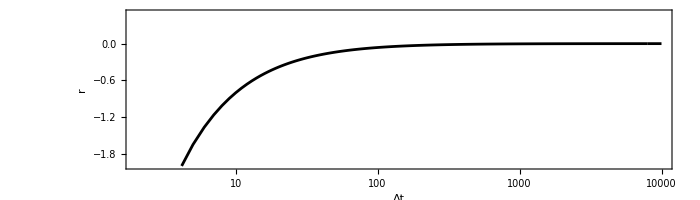

```mathematica
minmean[x_]:=Module[{n=Length[x]},ParallelTable[{j+1,Min[Table[Mean[x[[i;;i+j]]],{i,1,n-j}]]},{j,1,n-1}]];

ExtTime[t_,α_,N0_]:=r/.NSolve[1==N0 r/α Exp[r t]/(((r/α)-N0)+N0 Exp[r t]),r,Reals][[1]];N0=5000;
α=0.0001;
extlimit=ListLogLinearPlot[Quiet[ParallelTable[{t,ExtTime[t,α,N0]},{t,2,10000}]],ImageSize->700, AspectRatio->1/3.5,Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","r"},PlotStyle->Black,PlotRange->{{2,10000},{-2,.5}},Joined->True]
```

Calculate the running mean; skip to the next block of code if downloading existing files.

```mathematica
reps=100; (*100*)
length=10000; (*10000*)
μT=25;(*25*)
σT=4; (*4*)

whitereps=Table[minmean[w[SpecSynFourier[0,length,μT,σT]]],{reps}];
pinkreps=Table[minmean[w[SpecSynFourier[1,length,μT,σT]]],{reps}];
brownreps=Table[minmean[w[SpecSynFourier[2,length,μT,σT]]],{reps}];

Export[directory<>"windowing_r"<>ToString[reps]<>"_l"<>ToString[length]<>"_white.m",whitereps,"MX"]
Export[directory<>"windowing_r"<>ToString[reps]<>"_l"<>ToString[length]<>"_pink.m",pinkreps,"MX"]
Export[directory<>"windowing_r"<>ToString[reps]<>"_l"<>ToString[length]<>"_brown.m",brownreps,"MX"]
```

Import the MX files for the running mean.

```mathematica
whitereps=Import[directory<>"windowing_r100_l10000_white.m","MX"];
pinkreps=Import[directory<>"windowing_r100_l10000_pink.m","MX"];
brownreps=Import[directory<>"windowing_r100_l10000_brown.m","MX"];

length=10000;
meanwhite=Table[Mean[whitereps[[;;,i]]],{i,1,length-1}];
meanpink=Table[Mean[pinkreps[[;;,i]]],{i,1,length-1}];
meanbrown=Table[Mean[brownreps[[;;,i]]],{i,1,length-1}];
```

Plot Fig. 1d.

```mathematica
opac=0.03;
windowing=Show[
ListLogLinearPlot[brownreps,ImageSize->700, AspectRatio->1/3.5,PlotStyle->{{Darker[Darker[Red]],Directive[Opacity[opac]]}},Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","(r̄)_min"},PlotRange->{{2,10000},{-2,.5}},Joined->True,Epilog->{Text[Style["d)",Black,16],{.9,0.42}]}],
ListLogLinearPlot[pinkreps,PlotStyle->{{Lighter[Pink],Directive[Opacity[0.09]]}},Joined->True,PlotRange->Full],ListLogLinearPlot[whitereps,PlotStyle->{{Gray,Directive[Opacity[opac]]}},Joined->True,PlotRange->Full],ListLogLinearPlot[{meanwhite,meanpink,meanbrown},PlotStyle->{{Thick,Gray},{Thick,Lighter[Pink]},{Thick,Darker[Red]}},PlotRange->Full,Joined->True,PerformanceGoal->Accuracy, PlotLegends->Placed[{"White","Pink","Brown"},{Right,Bottom}]],
extlimit]

Export[directory<>"windowing_r100_l1000.pdf",windowing,ImageResolution->1000];
```